```mathematica
st0={1,0};st1={0,1};
st00=Flatten[KroneckerProduct[st0,st0]];
st01=Flatten[KroneckerProduct[st0,st1]];
st10=Flatten[KroneckerProduct[st1,st0]];
st11=Flatten[KroneckerProduct[st1,st1]];
M00=KroneckerProduct[st00,st00];
M01=KroneckerProduct[st01,st01];

M10=KroneckerProduct[st10,st10];
M11=KroneckerProduct[st11,st11];
```

```mathematica
psi=1/√2. ({{0}, {1}, {1}, {0}} );
rho[p_]:=p psi.Transpose[psi]+(1-p) IdentityMatrix[4]/4;
```

```mathematica
Tr[ConjugateTranspose[M00] rho[p] M00]
Tr[ConjugateTranspose[M01] rho[p] M01]
Tr[ConjugateTranspose[M10] rho[p] M10]
Tr[ConjugateTranspose[M11] rho[p] M11]
```

0.+(1-p)/4

(1-p)/4+0.5 p

(1-p)/4+0.5 p

0.+(1-p)/4

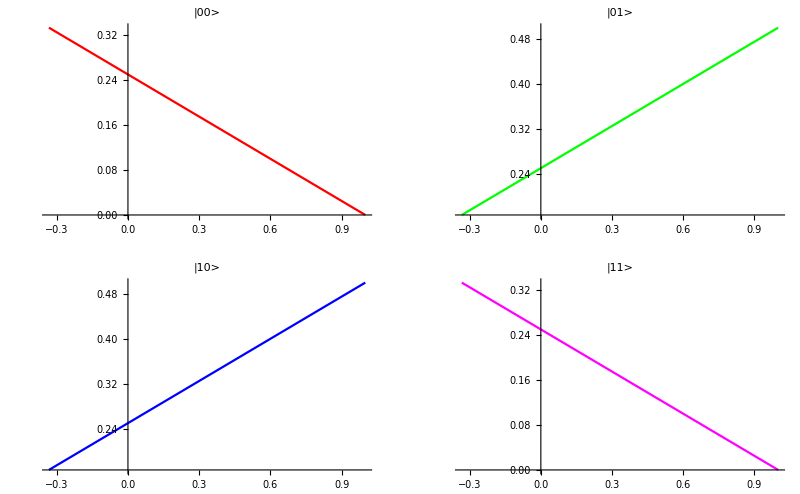

```mathematica
p1 = Plot[{Tr[ConjugateTranspose[M00]rho[p]M00] },{p,-0.333,1},PlotStyle -> Red, PlotLabel->"|00>"];
p2 = Plot[{Tr[ConjugateTranspose[M01]rho[p]M01]},{p,-0.333,1}, PlotStyle -> Green, PlotLabel->"|01>"];
p3 = Plot[{Tr[ConjugateTranspose[M10]rho[p]M10]},{p,-0.333,1}, PlotStyle -> Blue, PlotLabel->"|10>"];
p4 = Plot[{Tr[ConjugateTranspose[M11]rho[p]M11]},{p,-0.333,1}, PlotStyle -> Magenta, PlotLabel->"|11>"];
GraphicsGrid[{{p1,p2},{p3,p4}}]
```